```mathematica
xmin = -10.19;
xmax = -10.1;
ymax = 0.5;
ymin -0.45;
```

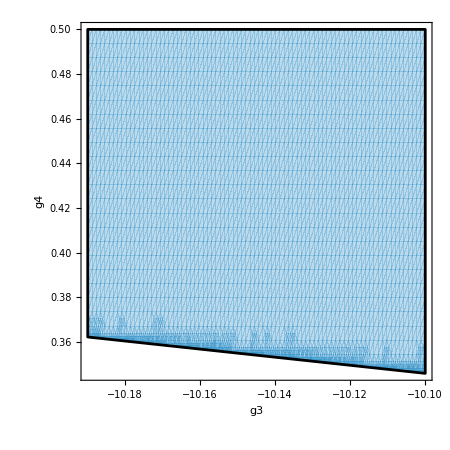

```mathematica
(*Replace condJ0 and condJ2 with your actual inequalities*)reg1=RegionPlot[g4+0.1810(g3+10.5)-0.4183>=0,{g3,xmin,xmax},{g4,ymin,ymax},PlotStyle->Directive[Opacity[.35]],BoundaryStyle->Black,PlotPoints->80,MaxRecursion->6,WorkingPrecision->30,Frame->True,FrameLabel->{"g3","g4"}];

Show[reg1,PlotRange->All,ImageSize->450]
```